## Integration Test

Define a set of functions to be integrated

Define a set of intervals on which `NIntegrate` should be performed

Measure the timing performance of both version of Mathematica

```mathematica
myFunction[k_,a_]:=Sum[i*a*Sin[#]^i,{i,k,0,-1}]&[x];
functionGrupx[n_,a_]:=Table[myFunction[k,a][x],{k,1,n}];
t25=Table[i,{i,1,25,1}];
t55=Table[i,{i,1,50,1}];
t75=Table[i,{i,1,75,1}];
t[ops_]:=Table[i,{i,1,ops,1}];
```

### Example with t

```mathematica
t[5]
t[12]
```

{1,2,3,4,5}

{1,2,3,4,5,6,7,8,9,10,11,12}

### Create threaded operation

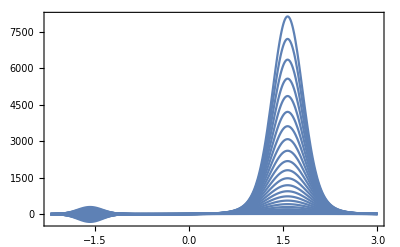

```mathematica
(*(list of functions)*)
thop[lister_]:=MapThread[myFunction,{lister,lister}];
Plot[thop[t25],{x,-2.2,3},PlotRange->Full,Frame->True,Axes->False]
```

### Example with thop (list of functions)

```mathematica
thop[t[0]]
thop[t[1]]
thop[t[3]]
```

{}

{Sin[x]}

{Sin[x],2 Sin[x]+4 Sin[x]^2,3 Sin[x]+6 Sin[x]^2+9 Sin[x]^3}

```mathematica
Do[Print[AbsoluteTiming[functionGrupx[100,1]][[1]]],{i,1,10,1}]
```

0.00627

0.006199

0.006145

0.0072

0.006033

0.006086

0.006039

0.006045

0.00614

0.005857

```mathematica
Do[Print[AbsoluteTiming[thop[t[125]]][[1]]],{i,1,10,1}]
```

0.009301

0.008442

0.009982

0.00917

0.009146

0.010012

0.009728

0.009688

0.008925

0.009501

```mathematica
thop[t[2]]
```

{Sin[x],2 Sin[x]+4 Sin[x]^2}

```mathematica
numint[function_,interval_]:=NIntegrate[function,{x,interval[[1]],interval[[2]]}];
```

```mathematica
batchintegrater[functions_,intervals_]:=Table[numint[functions[[i]],intervals[[i]]],{i,1,Length[functions]}];
```

```mathematica
intervalmaker[n_]:=Table[{-π,π/6},{i,1,n}];
```

```mathematica
intervalmaker[7]
```

{{-π,π/6},{-π,π/6},{-π,π/6},{-π,π/6},{-π,π/6},{-π,π/6},{-π,π/6}}

```mathematica
batchintegrater[thop[t[2]],intervalmaker[2]]
```

{-1.86603,2.73231}